```mathematica
(* 
 * Jaxton Maez
* CS 1410 Physics Simulator Project
* 12/6/19
*)

(* Copy the MathematicaData.txt file from the java project into the Wolfram Mathematica main folder. *)
```

```mathematica
Directory[]                        (* Use this to find where to put data file. *)
```

C:\Users\jaxtonmaez\Documents

```mathematica
data = Import["MathematicaData.txt","CSV"]            (*Import data*)
```

{{10.0006,999.941},{10.0012,999.883},{10.0018,999.824},{10.0023,999.766},{10.0029,999.707},{10.0035,999.648},{10.0041,999.589},{10.0047,999.531},{10.0053,999.472},{10.0059,999.413},{10.0065,999.354},{10.007,999.295},{10.0076,999.236},{10.0082,999.177},{10.0088,999.118},{10.0094,999.059},{10.01,999.},{10.0106,998.941},{10.0112,998.882},{10.0118,998.823},{10.0124,998.764},{10.013,998.705},{10.0135,998.645},{10.0141,998.586},{10.0147,998.527},{10.0153,998.468},{10.0159,998.408},{10.0165,998.349},{10.0171,998.29},{10.0177,998.23},{10.0183,998.171},{10.0189,998.111},{10.0195,998.052},{10.0201,997.992},{10.0207,997.933},{10.0213,997.873},{10.0219,997.813},{10.0225,997.754},{10.0231,997.694},{10.0237,997.634},{10.0243,997.575},{10.0249,997.515},{10.0254,997.455},{10.026,997.395},{10.0266,997.335},{10.0272,997.276},{10.0278,997.216},{10.0284,997.156},{10.029,997.096},{10.0296,997.036}}

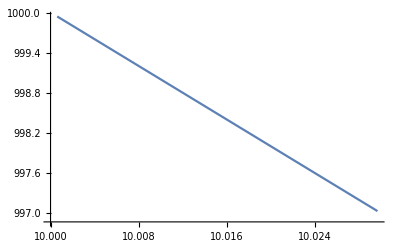

```mathematica
ListLinePlot[data]  (* simple plot of data *)
```